## CircularParticleDispersion By Aaron Becker, Daniel Bao, and

Particle Spread

```mathematica
Table[i,{i,0,2,.2}]
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.}

### step 1: draw circle and particles at a point. manipulate dispersion angle and movement direction. Show resulting arc

```mathematica
(*for masking background*)
pts={{0.,-0.5},{0.5,-0.5},{0.5,0.5},{0.,0.5},{-0.5,0.5},{-0.5,-0.5},{0.,-0.5}};
w={1,.5,.5,1,.5,.5,1};
k={0,0,0,1/4,1/2,1/2,3/4,1,1,1};
circleMask = (*a white donut with red edges, creates a blank spot in middle with radius 1*){White,EdgeForm[Red],FilledCurve[{{BSplineCurve[4pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]},{BSplineCurve[2pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]}}]};
```

```mathematica
Manipulate[DynamicModule[{pt,aL,aR,betaL,betaR,dispArc },
pt = {Cos[ptAng],Sin[ptAng]};
betaL= ArcTan[Sin[θ+disp]/Cos[θ+disp]]-ArcTan[-pt⟦2⟧/-pt⟦1⟧];
aL=If[Abs[betaL]>π/2, -π+Abs[ptAng]+2(θ+disp),ptAng-(π-2 betaL)];
betaR= ArcTan[Sin[θ-disp]/Cos[θ-disp]]-ArcTan[-pt⟦2⟧/-pt⟦1⟧];
aR=If[Abs[betaR]>π/2, -π+Abs[ptAng]+2(θ-disp),ptAng+ (π+2 betaR)];
(*Here's some code to modify for the bad cases we have.*)
If[(Abs[((θ+disp)-ptAng)]<=π/2),aL=ptAng,];
If[((θ+disp)+ptAng)>=π/2,aL=(π-2Abs[betaL])+ptAng(*aL=ptAng*),];If[((θ+disp)+ptAng)>=π/2&&ptAng>=0&&(θ+disp)≥π,aL=-((π-2Abs[betaL])-ptAng)(*aL=ptAng*),];
If[(Abs[((θ-disp)-ptAng)]<=π/2),aR=ptAng;,];
(*These are conditionals for the cases in which the ray is tangent/outside of the circle. We basically give the original point in that case!*)
(*Needs more conditionals for when the vector is pointing opposite of the circle!*)
(*If[θ==ptAng,aL=ptAng;aR=ptAng,];*)
aR=If[aL<aR,aR-2π, aR];
Graphics[{
 PointSize[Large], Black, Point[pt],

(*spread of particles*)
{LightBlue,Disk[pt,2,{θ-disp,θ+disp}]},
 (*hides stuff that extends beyond the circle*)circleMask,


(*movement dir*)
Blue,Arrow[{pt,pt+1/3{Cos[θ],Sin[θ]}}],
Orange,Thick,Circle[{0,0},.98,{aL,aR}],
{Green,Point[{Cos[aL],Sin[aL]}]},
{Purple,Point[{Cos[aR],Sin[aR]}]},
Black,
Text["aL: "<>ToString[aL],{0,0.1}],
Text[ToString[ArcTan[Sin[θ+disp]/Cos[θ+disp]]]<>"-"<>ToString[ArcTan[-pt⟦2⟧/-pt⟦1⟧]],{0,0.5}],
Text["aR: "<>ToString[aR],{0,-0.1}],
Text["betaL: "<>ToString[betaL],{0,0.2}],
Text["betaR: "<>ToString[betaR],{0,-0.2}],
Text[ToString[ArcTan[Sin[θ-disp]/Cos[θ-disp]]]<>"-"<>ToString[ArcTan[-pt⟦2⟧/-pt⟦1⟧]],{0,-0.5}]
(*Slight problem needed to fix when you need to switch aL and aR*)
},PlotRange->1.4{{-1,1},{-1,1}}]],
{disp,0,π/2,Appearance->"Labeled"},
{{θ,0},-π,π,Appearance->"Labeled"},
{{ptAng,0},-π,π,Appearance->"Labeled"}]
```

```mathematica
a={{-1,0},{0,1},{1,0}};
```

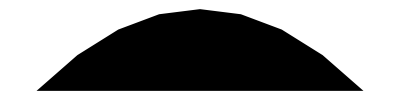

```mathematica
Graphics[FilledCurve[{BezierCurve[a]}]]
```

```mathematica
(*  (*these other ways didn't work so well.*)
{Opacity[0.5],Purple,If[aR<aL,Polygon[Append[Table[.99{Cos[a],Sin[a]},{a,aR,aL,(aL-aR)/20}],pt]]]},*)
(*
{Opacity[0.5],Purple,If[aR<aL,FilledCurve[{BSplineCurve[Table[{Cos[a],Sin[a]},{a,aR,aL,(aL-aR)/5}]]}]]},*)
```

### step 2: draw circle and particles along an arc. manipulate dispersion angle and movement direction. Show resulting arc.

```mathematica
pts={{0.,-0.5},{0.5,-0.5},{0.5,0.5},{0.,0.5},{-0.5,0.5},{-0.5,-0.5},{0.,-0.5}};
w={1,.5,.5,1,.5,.5,1};
k={0,0,0,1/4,1/2,1/2,3/4,1,1,1};
circleMask = (*a white donut with red edges, creates a blank spot in middle with radius 1*){White,EdgeForm[Red],FilledCurve[{{BSplineCurve[4pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]},{BSplineCurve[2pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]}}]};
Graphics[circleMask]
```

-Graphics-